```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];

(*ResourceFunction["MaTeXInstall"][]*)
(* Needs["PacletManager`"]
PacletInstall["/full/path/to/MaTeX-1.7.9.paclet"] *)
(* Need to run the syntax above for new mathematica versions to install MaTeX *)
```

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}"}];
{"BasePreamble"->{"\\usepackage{lmodern,exscale}","\\usepackage{amsmath,amssymb}"},"Preamble"->{"\\usepackage{xcolor,txfonts}"},"DisplayStyle"->True,ContentPadding->True,LineSpacing->{1.2,0},FontSize->12,Magnification->1,"LogFileFunction"->None,"TeXFileFunction"->None};
texStyle={FontFamily->"Latin Modern Roman",FontSize->9};
```

```mathematica
(****** Parameter choices to pick from ******)
```

```mathematica
m = {10^-15,10^-20,10^-25,10^-30,10^-35}; (** A list of mass values you can pick from, defined with respect to Subscript[H, inf] ***)
xrh = Table[m[[i]]^(-1/2),{i,1,Length[m]}];
yend = Table[m[[i]]^(1/2),{i,1,Length[m]}]; (*** y = a/a_* so yend denotes the beginning of RDU or the end of inflation ***)
asqI= {10^4,10^5,10^6};
```

```mathematica
(** The variables we set above are defined as ***)
```

```mathematica
MaTeX["\\begin{aligned}
\\alpha_{\\rm I}^2 \\equiv \\frac{\\alpha^2 H_{\\rm I}^2}{m^2}, \\quad y_{\\rm end} = \\sqrt{\\frac{m}{H_{\\rm I}}}, \\quad x_{\\rm rh} = \\frac{k_{\\rm rh}}{k_*}
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\begin{aligned}
\\textrm{The time variable is defined as:}\\quad y = \\frac{a}{a_*}\\quad \\textrm{where} \\quad H(a_*) = m\\quad \\textrm{during RDU}
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
(** Set some indexes to chose from the list of parameters we defined above**)
```

```mathematica
yindex = 2;
aindex = 3;
```

```mathematica
(** k_end or k_rh for each choice of mass we define above, for smaller m/H_inf ratio, k_rh becomes larger **)
Print["The scales that exit the horizon at the end of inflation for the mass choices we pick above: " , N[xrh]]
```

The scales that exit the horizon at the end of inflation for the mass choices we pick above: {3.16228×10^7,1.×10^10,3.16228×10^12,1.×10^15,3.16228×10^17}

```mathematica
ytc = (1/3)^(1/4)asqI[[aindex]]^(1/4)yend[[yindex]]; (** Larger the Subscript[α, I] longer the duration of the transient tachyonic era ***)
```

```mathematica
MaTeX["\\begin{aligned}
y_{\\rm tc}\\equiv w^{1/4} \\sqrt{\\alpha_{\\rm I}}\\,\\, y_{\\rm end}\\quad \\textrm{where} \\quad w = 1/3
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
Print["The time when inflation ends/RDU begins: ",N[yend[[yindex]]]]
```

The time when inflation ends/RDU begins: 3.16228×10^-8

```mathematica
Print["The time when the tachyonic phase ends during RDU: ",N[ytc]]
```

The time when the tachyonic phase ends during RDU: 7.59836×10^-7

```mathematica
MaTeX["\\begin{aligned}
\\textrm{The scales that re-enters the horizon during RDU satisfies:}\\quad k = a_{\\rm re} H(a_{\\rm re}) \\Longrightarrow x_* = y_{\\rm re}^{-1}
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\begin{aligned}
\\textrm{So the scale that re-enters the horizon at the end of tachyonic phase satisfies:}\\quad x_* = y_{\\rm tc}^{-1}
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
Print["The scale that re-enters the horizon when the tachyonic phase ends during RDU: ",N[ytc^-1]] (* i.e k_c / k_* *)
```

The scale that re-enters the horizon when the tachyonic phase ends during RDU: 1.31607×10^6

```mathematica
Print["The scale that exit the horizon at the end of inflation for the mass choice we pick above: " , N[xrh[[yindex]]]]
```

The scale that exit the horizon at the end of inflation for the mass choice we pick above: 3.16228×10^7

```mathematica
MaTeX["\\begin{aligned}
\\textrm{During the RDU the transverse modes satisfies the following mode equation:}\\quad A_T''(y) + \\left[x_*^2 + y^2 \\left(1 - \\frac{\\alpha(y)^2}{3}\\right)\\right] A_T(y) = 0,
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\begin{aligned}
\\textrm{where:}\\quad \\alpha(y)^2 = \\alpha_{\\rm I}^2 \\left(\\frac{y_{\\rm end}}{y}\\right)^4 \\quad \\textrm{implying modes can exhibit tachyonic instability when}\\quad \\alpha(y)^2 > 3 \\quad \\textrm{or for:} \\quad y < y_{\\rm tc} = 3^{-1/4} \\sqrt{\\alpha_{\\rm I}}\\,\\, y_{\\rm end}
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\begin{aligned}
\\textrm{since}\\quad \\alpha(y_{\\rm end})^2 = \\alpha_{\\rm I}^2 \\gg 1 \\quad \\textrm{we expect certain modes $x_*$ to have a negative mass during}\\quad y_{\\rm end} < y < y_{\\rm tc}
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\begin{aligned}
\\textrm{In particular, within this time interval modes that satisfy:}\\quad x_* < \\frac{\\alpha_{\\rm I}}{\\sqrt{3}}\\,\\, \\frac{y_{\\rm end}^2}{y}\\quad \\textrm{will exhibit negative mass and hence tachyonic instability}
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
MaTeX["\\begin{aligned}
\\textrm{Considering the boundary of the tachyonic regime, modes that satisfy:}\\quad x_* < \\frac{\\alpha_{\\rm I}}{\\sqrt{3}}\\, y_{\\rm end}\\quad \\textrm{or}\\quad x_* < \\frac{\\sqrt{\\alpha_{\\rm I}}}{3^{1/4}}\\,y_{\\rm end}
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
xst1 = asqI[[aindex]]^(1/2)/(√3)yend[[yindex]];
xst2 = asqI[[aindex]]^(1/4)/3^(1/4)yend[[yindex]];
```

```mathematica
Print["Modes that could be tachyonic should be smaller than: " , N[xst1]]
```

Modes that could be tachyonic should be smaller than: 5.7735×10^-8

```mathematica
Print["or: " , N[xst2]]
```

or: 2.40281×10^-9

```mathematica
(*** Generate a grid of scales that satisty x_* < xst1 also including scales that satisfy x_* < xst1 **)
```

```mathematica
xssin=10^-1 xst2;         (*1.*)
xssend=xst1; (*xrh[[yindex]]*)
xssnum=50;
Do[xss[i]=xssin(xssend/xssin)^((i-1)/(xssnum-1)),{i,1,xssnum}]
N[Table[xss[i],{i,1,xssnum}]]
```

{2.40281×10^-10,2.68724×10^-10,3.00533×10^-10,3.36107×10^-10,3.75893×10^-10,4.20388×10^-10,4.7015×10^-10,5.25802×10^-10,5.88042×10^-10,6.5765×10^-10,7.35497×10^-10,8.22559×10^-10,9.19926×10^-10,1.02882×10^-9,1.1506×10^-9,1.2868×10^-9,1.43912×10^-9,1.60947×10^-9,1.79999×10^-9,2.01306×10^-9,2.25134×10^-9,2.51784×10^-9,2.81588×10^-9,3.1492×10^-9,3.52198×10^-9,3.93888×10^-9,4.40513×10^-9,4.92657×10^-9,5.50974×10^-9,6.16193×10^-9,6.89133×10^-9,7.70707×10^-9,8.61937×10^-9,9.63966×10^-9,1.07807×10^-8,1.20568×10^-8,1.3484×10^-8,1.50802×10^-8,1.68652×10^-8,1.88616×10^-8,2.10943×10^-8,2.35912×10^-8,2.63838×10^-8,2.95068×10^-8,3.29996×10^-8,3.69058×10^-8,4.12744×10^-8,4.61601×10^-8,5.16242×10^-8,5.7735×10^-8}

```mathematica
(*** Lets plot the dispersion relation for these modes to prove that frequency square of them are negative for a certain time interval ***)
```

```mathematica
wsq[xs_,asq_,ye_,y_]:=xs^2 +y^2 (1-asq(ye/y)^4/3);
```

```mathematica
(*** İF THE INDEX OF XSS smaller, mode spend more time in the tachyonic region, end of which is denoted by dotted red vertical line ***)
```

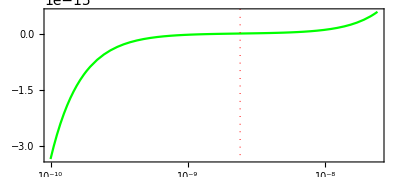

```mathematica
LogLinearPlot[{wsq[xss[1],asqI[[aindex]],yend[[yindex]],t]},{t,yend[[yindex]],10ytc },PlotRange->All,PlotStyle->{Green},BaseStyle->texStyle,FrameStyle->BlackFrame,FrameLabel->MaTeX/@{"y = a/a_*","w_{*}^2"},RotateLabel->False, AspectRatio-> 4/9,Frame->True,Epilog->{Red,Dotted,Line[{{Log[ytc],Log[10^-50]},{Log[ytc],Log[100]}}]}]
```

```mathematica
(*** For modes smaller than xst1, we do not expect negative frequency squared, lets check this ***)
```

```mathematica
xssain=xst1;         (*1.*)
xssaend=100 xst1; (*xrh[[yindex]]*)
xssanum=50;
Do[xssa[i]=xssain(xssaend/xssain)^((i-1)/(xssanum-1)),{i,1,xssanum}]
N[Table[xssa[i],{i,1,xssanum}]]
```

{5.7735×10^-8,6.34243×10^-8,6.96742×10^-8,7.654×10^-8,8.40823×10^-8,9.23679×10^-8,1.0147×10^-7,1.11469×10^-7,1.22453×10^-7,1.3452×10^-7,1.47776×10^-7,1.62338×10^-7,1.78334×10^-7,1.95908×10^-7,2.15213×10^-7,2.3642×10^-7,2.59717×10^-7,2.8531×10^-7,3.13425×10^-7,3.4431×10^-7,3.78239×10^-7,4.15511×10^-7,4.56456×10^-7,5.01435×10^-7,5.50847×10^-7,6.05128×10^-7,6.64758×10^-7,7.30264×10^-7,8.02226×10^-7,8.81278×10^-7,9.6812×10^-7,1.06352×10^-6,1.16832×10^-6,1.28345×10^-6,1.40992×10^-6,1.54886×10^-6,1.70148×10^-6,1.86915×10^-6,2.05333×10^-6,2.25567×10^-6,2.47795×10^-6,2.72213×10^-6,2.99037×10^-6,3.28505×10^-6,3.60876×10^-6,3.96437×10^-6,4.35502×10^-6,4.78417×10^-6,5.25561×10^-6,5.7735×10^-6}

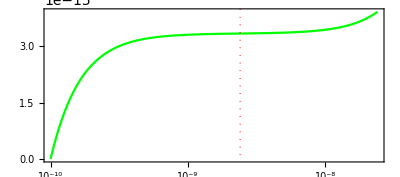

```mathematica
LogLinearPlot[{wsq[xssa[1],asqI[[aindex]],yend[[yindex]],t]},{t,yend[[yindex]],10ytc },PlotRange->All,PlotStyle->{Green},BaseStyle->texStyle,FrameStyle->BlackFrame,FrameLabel->MaTeX/@{"y = a/a_*","w_{*}^2"},RotateLabel->False, AspectRatio-> 4/9,Frame->True,Epilog->{Red,Dotted,Line[{{Log[ytc],Log[10^-50]},{Log[ytc],Log[100]}}]}]
```

```mathematica
(***************************************************************************************************************************************)
```

```mathematica
(* We will first generate initial conditions (IC) for these modes from the inflation side. These IC's will serve as input for the evolution during RDU *)
```

```mathematica
MaTeX["\\begin{aligned}
\\textrm{EoM during Inflation:}\\quad \\tilde{A}_T''(y) + \\frac{2}{y}\\tilde{A}_T'(y) + \\left[\\frac{x_*^2\\, y_{\\rm end}^4}{y^4} + \\frac{y_{\\rm end}^4}{y^2} \\left(1 + \\alpha_{\\rm I}^2\\right)\\right] \\tilde{A}_T(y) = 0,\\quad\\quad \\tilde{A}_T \\equiv \\sqrt{2k}\\, A_T
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
eq1INF[y_]:=ATp[y]-AT'[y];
eq2INF[y_,xs_,ye_,asq_]:=ATp'[y]+2/y ATp[ y]+((xs^2 ye^4)/y^4+ye^4/y^2(1+asq) )AT[y];
```

```mathematica
(****  Solve the system starting from the 4 e-folds before horizon exit during inflation until the end of inflation/beginning of RDU, to generate initial conditions for RDU ****)
```

```mathematica
Do[Clear[stff];
stff =NDSolve[{eq1INF[y]==0,eq2INF[y,xss[i],yend[[yindex]],asqI[[aindex]]]==0,AT[xss[i] yend[[yindex]]^2 Exp[-4]]==Exp[ⅈ Exp[4]],ATp[xss[i] yend[[yindex]]^2 Exp[-4]]==- ⅈ(xss[i] yend[[yindex]]^2 Exp[-8])^-1 Exp[ⅈ Exp[4]]},{AT,ATp},{y,xss[i] yend[[yindex]]^2 Exp[-4],yend[[yindex]]}];
ATin[i] =AT[yend[[yindex]]]/.stff[[1]];
ATpin[i]=ATp[yend[[yindex]]]/.stff[[1]];
,{i,1,xssnum}]
```

```mathematica
(*** Standard case where non-minimal coupling is not present, i.e α = 0 or Subscript[α, I] = α Subscript[H, I]/m = 0 ***)
```

```mathematica
Do[Clear[stffa];
stffa =NDSolve[{eq1INF[y]==0,eq2INF[y,xss[i],yend[[yindex]],0]==0,AT[xss[i] yend[[yindex]]^2 Exp[-4]]==Exp[ⅈ Exp[4]],ATp[xss[i] yend[[yindex]]^2 Exp[-4]]==- ⅈ(xss[i] yend[[yindex]]^2 Exp[-8])^-1 Exp[ⅈ Exp[4]]},{AT,ATp},{y,xss[i] yend[[yindex]]^2 Exp[-4],yend[[yindex]]}];
ATina[i] =AT[yend[[yindex]]]/.stffa[[1]];
ATpina[i]=ATp[yend[[yindex]]]/.stffa[[1]];
,{i,1,xssnum}]
```

```mathematica
Table[ATin[i],{i,1,xssnum}]
```

{1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ}

```mathematica
Table[ATina[i],{i,1,xssnum}]
```

{1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ,1.+7.14305×10^-8 ⅈ}

```mathematica
Table[ATpin[i],{i,1,xssnum}]
```

{5.61441×10^-18-2.25619×10^-10 ⅈ,6.31741×10^-18-2.5387×10^-10 ⅈ,6.91809×10^-18-2.78009×10^-10 ⅈ,7.76373×10^-18-3.11991×10^-10 ⅈ,8.7342×10^-18-3.50991×10^-10 ⅈ,9.77762×10^-18-3.92921×10^-10 ⅈ,1.08608×10^-17-4.36451×10^-10 ⅈ,1.22079×10^-17-4.90582×10^-10 ⅈ,1.37073×10^-17-5.5084×10^-10 ⅈ,1.53369×10^-17-6.16326×10^-10 ⅈ,1.72615×10^-17-6.93665×10^-10 ⅈ,1.91611×10^-17-7.70004×10^-10 ⅈ,2.15413×10^-17-8.65652×10^-10 ⅈ,2.41963×10^-17-9.72348×10^-10 ⅈ,2.71094×10^-17-1.08941×10^-9 ⅈ,3.00484×10^-17-1.20752×10^-9 ⅈ,3.3859×10^-17-1.36065×10^-9 ⅈ,3.79623×10^-17-1.52555×10^-9 ⅈ,4.25197×10^-17-1.70869×10^-9 ⅈ,4.81514×10^-17-1.935×10^-9 ⅈ,5.31422×10^-17-2.13556×10^-9 ⅈ,5.96062×10^-17-2.39532×10^-9 ⅈ,6.67488×10^-17-2.68235×10^-9 ⅈ,7.51303×10^-17-3.01917×10^-9 ⅈ,8.33027×10^-17-3.34759×10^-9 ⅈ,9.36823×10^-17-3.76469×10^-9 ⅈ,1.05308×10^-16-4.23187×10^-9 ⅈ,1.17875×10^-16-4.73689×10^-9 ⅈ,1.3353×10^-16-5.36601×10^-9 ⅈ,1.47316×10^-16-5.92×10^-9 ⅈ,1.65309×10^-16-6.64307×10^-9 ⅈ,1.85103×10^-16-7.43852×10^-9 ⅈ,2.08102×10^-16-8.36272×10^-9 ⅈ,2.30986×10^-16-9.28236×10^-9 ⅈ,2.5992×10^-16-1.04451×10^-8 ⅈ,2.91922×10^-16-1.17311×10^-8 ⅈ,3.26659×10^-16-1.3127×10^-8 ⅈ,3.62664×10^-16-1.45739×10^-8 ⅈ,4.08134×10^-16-1.64012×10^-8 ⅈ,4.57556×10^-16-1.83872×10^-8 ⅈ,5.13058×10^-16-2.06176×10^-8 ⅈ,5.76905×10^-16-2.31833×10^-8 ⅈ,6.40292×10^-16-2.57306×10^-8 ⅈ,7.2044×10^-16-2.89514×10^-8 ⅈ,8.08384×10^-16-3.24856×10^-8 ⅈ,9.07602×10^-16-3.64727×10^-8 ⅈ,1.00522×10^-15-4.03954×10^-8 ⅈ,1.13186×10^-15-4.54845×10^-8 ⅈ,1.27261×10^-15-5.11407×10^-8 ⅈ,1.42739×10^-15-5.73609×10^-8 ⅈ}

```mathematica
Table[ATpina[i],{i,1,xssnum}]
```

{5.61441×10^-18-2.25619×10^-10 ⅈ,6.31741×10^-18-2.5387×10^-10 ⅈ,6.91809×10^-18-2.78009×10^-10 ⅈ,7.76373×10^-18-3.11991×10^-10 ⅈ,8.7342×10^-18-3.50991×10^-10 ⅈ,9.77762×10^-18-3.92921×10^-10 ⅈ,1.08608×10^-17-4.36451×10^-10 ⅈ,1.22079×10^-17-4.90582×10^-10 ⅈ,1.37073×10^-17-5.5084×10^-10 ⅈ,1.53369×10^-17-6.16326×10^-10 ⅈ,1.72615×10^-17-6.93665×10^-10 ⅈ,1.91611×10^-17-7.70004×10^-10 ⅈ,2.15413×10^-17-8.65652×10^-10 ⅈ,2.41963×10^-17-9.72348×10^-10 ⅈ,2.71094×10^-17-1.08941×10^-9 ⅈ,3.00484×10^-17-1.20752×10^-9 ⅈ,3.3859×10^-17-1.36065×10^-9 ⅈ,3.79623×10^-17-1.52555×10^-9 ⅈ,4.25197×10^-17-1.70869×10^-9 ⅈ,4.81514×10^-17-1.935×10^-9 ⅈ,5.31422×10^-17-2.13556×10^-9 ⅈ,5.96062×10^-17-2.39532×10^-9 ⅈ,6.67488×10^-17-2.68235×10^-9 ⅈ,7.51303×10^-17-3.01917×10^-9 ⅈ,8.33027×10^-17-3.34759×10^-9 ⅈ,9.36823×10^-17-3.76469×10^-9 ⅈ,1.05308×10^-16-4.23187×10^-9 ⅈ,1.17875×10^-16-4.73689×10^-9 ⅈ,1.3353×10^-16-5.36601×10^-9 ⅈ,1.47316×10^-16-5.92×10^-9 ⅈ,1.65309×10^-16-6.64307×10^-9 ⅈ,1.85103×10^-16-7.43852×10^-9 ⅈ,2.08102×10^-16-8.36272×10^-9 ⅈ,2.30986×10^-16-9.28236×10^-9 ⅈ,2.5992×10^-16-1.04451×10^-8 ⅈ,2.91922×10^-16-1.17311×10^-8 ⅈ,3.26659×10^-16-1.3127×10^-8 ⅈ,3.62664×10^-16-1.45739×10^-8 ⅈ,4.08134×10^-16-1.64012×10^-8 ⅈ,4.57556×10^-16-1.83872×10^-8 ⅈ,5.13058×10^-16-2.06176×10^-8 ⅈ,5.76905×10^-16-2.31833×10^-8 ⅈ,6.40292×10^-16-2.57306×10^-8 ⅈ,7.2044×10^-16-2.89514×10^-8 ⅈ,8.08384×10^-16-3.24856×10^-8 ⅈ,9.07602×10^-16-3.64727×10^-8 ⅈ,1.00522×10^-15-4.03954×10^-8 ⅈ,1.13186×10^-15-4.54845×10^-8 ⅈ,1.27261×10^-15-5.11407×10^-8 ⅈ,1.42739×10^-15-5.73609×10^-8 ⅈ}

```mathematica
(**** Notice that initial condition generated is the same for the standard case of α = 0 as well *****)
```

```mathematica
(*** Now solve for the evolution during RDU ***)
```

```mathematica
MaTeX["\\begin{aligned}
\\textrm{EoM during RDU:}\\quad \\tilde{A}_T''(y) + \\left[x_*^2 + y^2 \\left(1 - \\frac{\\alpha(y)^2}{3}\\right)\\right] \\tilde{A}_T(y) = 0,\\quad\\quad \\tilde{A}_T \\equiv \\sqrt{2k}\\, A_T
\\end{aligned}",Magnification->2]
```

-Graphics-

```mathematica
eq1RDU[y_]:=ATp[y]-AT'[y];
 eq2RDU[y_,xs_,ye_,asq_]:=ATp'[y]+(xs^2 +y^2 (1-asq(ye/y)^4/3))AT[y];
```

```mathematica
yre = Table[xss[i]^-1,{i,1,xssnum}] ;(*** Time of horizon re-entry for individual modes, change it depending on x_* = k/k_* you are evaluating ***)
ynr =  Table[xss[i],{i,1,xssnum}];(*** The time during RDU when the individual mode becomes non-relativistic, i.e k = a m. Note that depending on the choice of parameters they can become non-relativistic during Inflation,  ****)
```

```mathematica
Print["Horizon re-entry times of the modes we picked is quite late, because these modes are relatively large modes as compared to k_*: ",N[yre]]
```

Horizon re-entry times of the modes we picked is quite late, because these modes are relatively large modes as compared to k_*: {4.16179×10^9,3.7213×10^9,3.32742×10^9,2.97524×10^9,2.66033×10^9,2.37876×10^9,2.12698×10^9,1.90186×10^9,1.70056×10^9,1.52057×10^9,1.35963×10^9,1.21572×10^9,1.08704×10^9,9.71988×10^8,8.6911×10^8,7.77121×10^8,6.94868×10^8,6.21321×10^8,5.55559×10^8,4.96757×10^8,4.44179×10^8,3.97166×10^8,3.55129×10^8,3.17541×10^8,2.83931×10^8,2.53879×10^8,2.27008×10^8,2.02981×10^8,1.81497×10^8,1.62287×10^8,1.4511×10^8,1.29751×10^8,1.16018×10^8,1.03738×10^8,9.27582×10^7,8.29404×10^7,7.41618×10^7,6.63123×10^7,5.92936×10^7,5.30178×10^7,4.74063×10^7,4.23886×10^7,3.79021×10^7,3.38904×10^7,3.03034×10^7,2.7096×10^7,2.42281×10^7,2.16637×10^7,1.93708×10^7,1.73205×10^7}

```mathematica
Print["The time when the chosen modes becomes non-relativistic is quite early in the RDU: ",N[ynr]]
```

The time when the chosen modes becomes non-relativistic is quite early in the RDU: {2.40281×10^-10,2.68724×10^-10,3.00533×10^-10,3.36107×10^-10,3.75893×10^-10,4.20388×10^-10,4.7015×10^-10,5.25802×10^-10,5.88042×10^-10,6.5765×10^-10,7.35497×10^-10,8.22559×10^-10,9.19926×10^-10,1.02882×10^-9,1.1506×10^-9,1.2868×10^-9,1.43912×10^-9,1.60947×10^-9,1.79999×10^-9,2.01306×10^-9,2.25134×10^-9,2.51784×10^-9,2.81588×10^-9,3.1492×10^-9,3.52198×10^-9,3.93888×10^-9,4.40513×10^-9,4.92657×10^-9,5.50974×10^-9,6.16193×10^-9,6.89133×10^-9,7.70707×10^-9,8.61937×10^-9,9.63966×10^-9,1.07807×10^-8,1.20568×10^-8,1.3484×10^-8,1.50802×10^-8,1.68652×10^-8,1.88616×10^-8,2.10943×10^-8,2.35912×10^-8,2.63838×10^-8,2.95068×10^-8,3.29996×10^-8,3.69058×10^-8,4.12744×10^-8,4.61601×10^-8,5.16242×10^-8,5.7735×10^-8}

```mathematica
yeq=(Sqrt[m[[yindex]]^-1]Sqrt[(1.62 10^-37)/10^14])^-1 ;(** Time of matter radiation equality for a given m/H_I **)
```

```mathematica
Print["The time of matter radiation equality vs horizon re-entry time of the largest mode we consider: ", N[yeq]," vs ",N[yre[[1]]]]
```

The time of matter radiation equality vs horizon re-entry time of the largest mode we consider: 2.48452×10^15 vs 4.16179×10^9

```mathematica
If[N[yre[[1]]]<yeq,Print["Horizon re-entry of the largest mode we consider is earlier than the time of matter radiation equality"],Print["The largest mode re-enters during MDU"]]
```

Horizon re-entry of the largest mode we consider is earlier than the time of matter radiation equality

```mathematica
(*** Set a final time for NDSolve depending on the parameter choices you make. This is required because depending on the parameter choices modes may start to oscillate a lot slowing down the solver ***)
```

```mathematica
Do[
sol[i]=NDSolve[{eq1RDU[y]==0,eq2RDU[y,xss[i],yend[[yindex]],asqI[[aindex]]]==0,AT[yend[[yindex]]]== ATin[i],ATp[yend[[yindex]]]==ATpin[i]},{AT,ATp},{y,yend[[yindex]],5}, Method->"BDF", AccuracyGoal->20,PrecisionGoal->12,MaxStepSize->0.001]
,{i,1,xssnum}]
```

```mathematica
Do[
sola[i]=NDSolve[{eq1RDU[y]==0,eq2RDU[y,xss[i],yend[[yindex]],0]==0,AT[yend[[yindex]]]== ATin[i],ATp[yend[[yindex]]]==ATpin[i]},{AT,ATp},{y,yend[[yindex]],5}, Method->"BDF", AccuracyGoal->20,PrecisionGoal->12,MaxStepSize->0.001]
,{i,1,xssnum}]
```

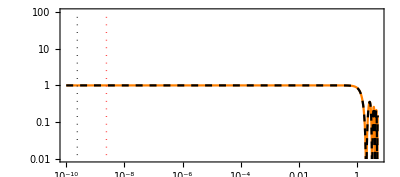
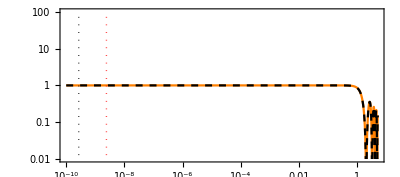
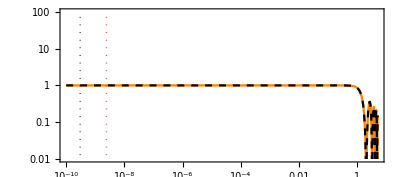
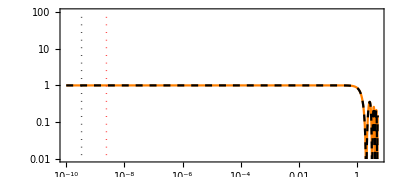
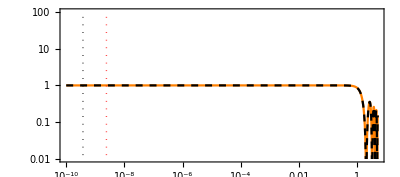
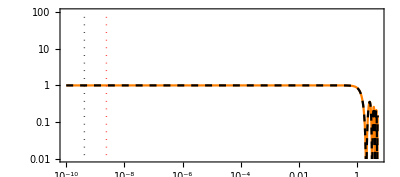
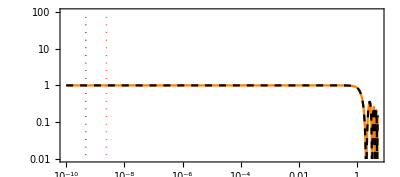
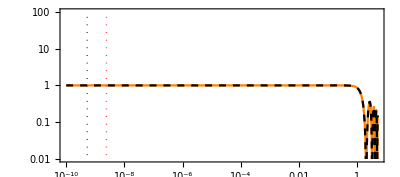

```mathematica
Table[LogLogPlot[{Abs[AT[t]/.sol[i]]^2,Abs[AT[t]/.sola[i]]^2},{t,yend[[yindex]],5},PlotRange->{Automatic,{Abs[ATin[i]]^2/100,Abs[ATin[i]]^2 100}},PlotStyle->{Orange,{Black,Dashed}},BaseStyle->texStyle,FrameStyle->BlackFrame,FrameLabel->MaTeX/@{"y = a/a_*","\\Big|\\sqrt{2k}\,A_T\,\\Big|^2"},RotateLabel->False, AspectRatio-> 4/9,Frame->True,Epilog->{Purple,Dashed,Line[{{Log[yre[[i]]],Log[10^-40]},{Log[yre[[i]]],Log[100]}}],Red,Dotted,Line[{{Log[ytc],Log[10^-50]},{Log[ytc],Log[100]}}],Black,Dotted,Line[{{Log[ynr[[i]]],Log[10^-40]},{Log[ynr[[i]]],Log[100]}}]}],{i,1,50}]
```

```mathematica
(*** RED DOTTED LINES DENOTE THE END OF TACHYONIC ERA WHILE BLACK LINES DENOTE THE TIME WHEN THE MODES BECOME NON-RELATIVISTIC ***)
(*** WE SEE FROM THE ABOVE PLOTS THAT
```

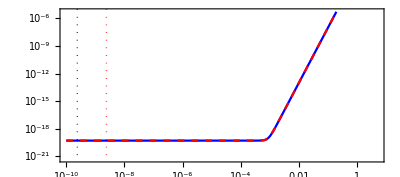
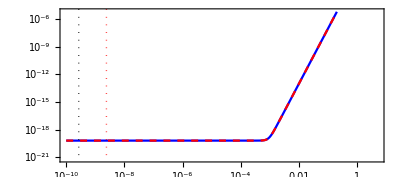
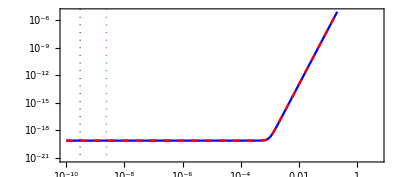
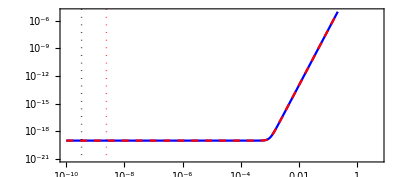
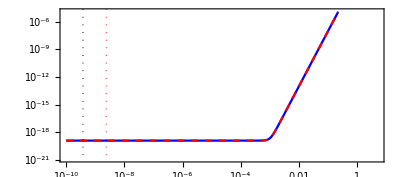
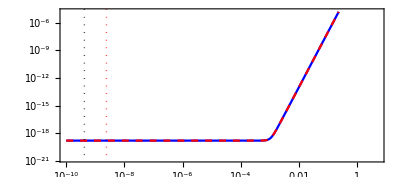
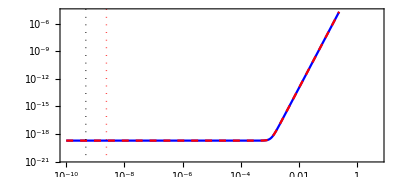
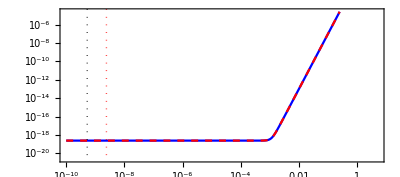

```mathematica
Table[LogLogPlot[{Abs[ATp[t]/.sol[i]]^2,Abs[ATp[t]/.sola[i]]^2},{t,yend[[yindex]],5},PlotRange->{Automatic,{Abs[ATpin[i]]^2/100,Abs[ATpin[i]]^2 10^14}},PlotStyle->{Blue,{Red,Dashed}},BaseStyle->texStyle,FrameStyle->BlackFrame,FrameLabel->MaTeX/@{"y = a/a_*","\\Big|\\sqrt{2k}\,A_T'\,\\Big|^2"},RotateLabel->False, AspectRatio-> 4/9,Frame->True,Epilog->{Purple,Dashed,Line[{{Log[yre[[i]]],Log[10^-40]},{Log[yre[[i]]],Log[100]}}],Red,Dotted,Line[{{Log[ytc],Log[10^-50]},{Log[ytc],Log[100]}}],Black,Dotted,Line[{{Log[ynr[[i]]],Log[10^-40]},{Log[ynr[[i]]],Log[100]}}]}],{i,1,50}]
```